-Graphics-

Distribution Of the rates:

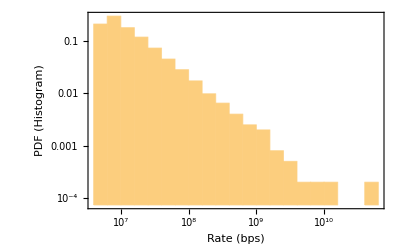

```mathematica
f[α_,β_]:=β*(1/(1-RandomVariate[UniformDistribution[{0.001,0.999}]]))^(1/α);
g[α_,β_,x_]:=Min[40*10^9,x*β*(1/(1-RandomVariate[UniformDistribution[]]))^(1/α)];
descriptivestatistics[data_]:={{"Mean","Median","Stdv.","Skewness","Kurtosis"},{Mean[data],Median[data],StandardDeviation[data],Skewness[data],Kurtosis[data]}}//Transpose//Grid//Panel;
list=Table[(
Subscript[l, i]=Table[g[1.0256410256410255,10^6,5*10^(i-1)],{j,10000}];
Subscript[h, i] = GraphicsGrid[{{Histogram[Subscript[l, i],"Log","LogProbability",FrameLabel->{"Rate (bps)","PDF (Histogram)"},Frame->True],descriptivestatistics@Subscript[l, i]}},ImageSize->Full]
),{i,1,4}];
list[[1]]
```

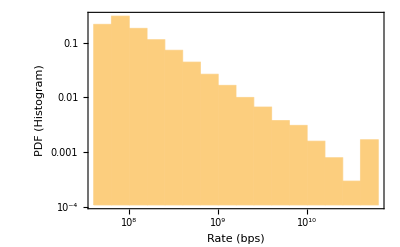

```mathematica
list[[2]]
```

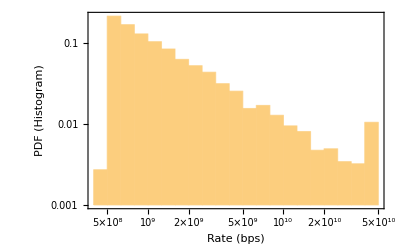

```mathematica
list[[3]]
```

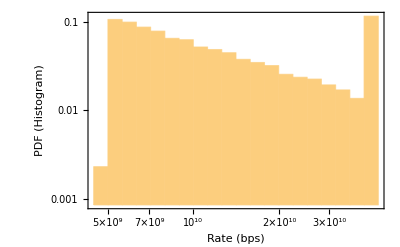

```mathematica
list[[4]]
```

Distribution Of the sizes and packet types:

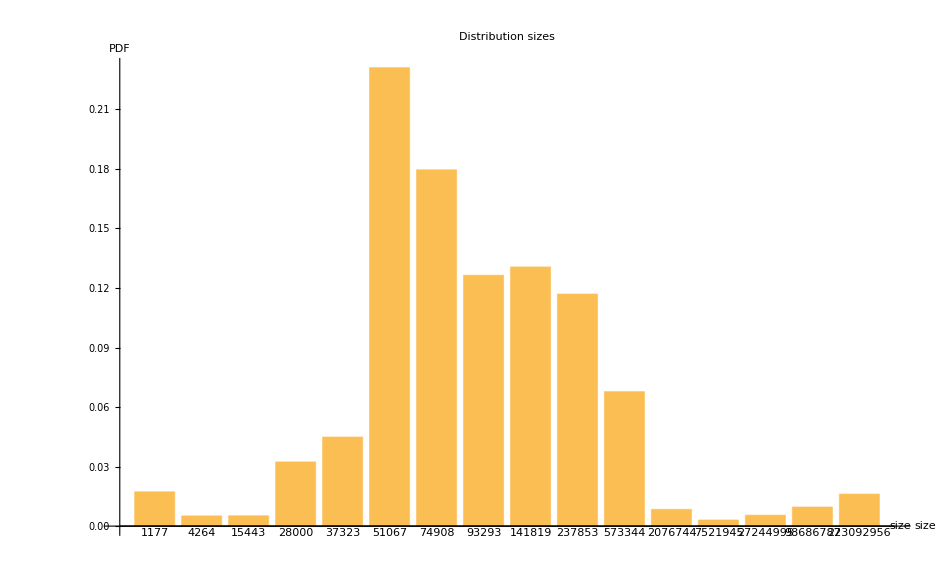

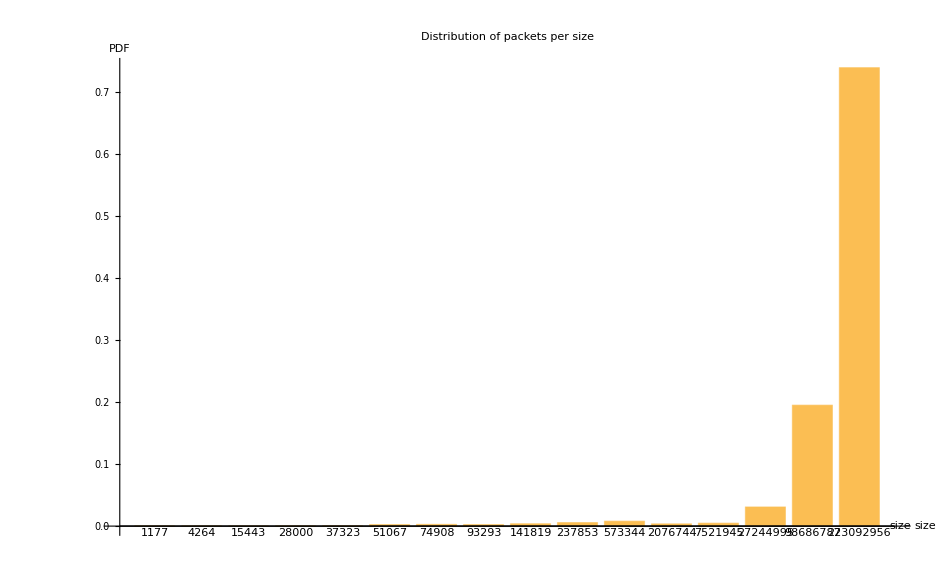

```mathematica
sizes = {1177 ,4264 ,15443 ,28000 ,37323 ,51067 ,74908 ,93293 ,141819 ,237853 ,573344 ,2076744 ,7521945 ,27244995 ,98686787 ,223092956};
distOfSizes = {0.01728594,0.005140236,0.005232129,0.032341695,0.044879491,0.231028785,0.179568695,0.126417652,0.130605671,0.116946187,0.067761784,0.008431136,0.003078399,0.005519292,0.009625739,0.016137169};
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]]

Print[BarChart[Table[N[(distOfSizes[[j]]*sizes[[j]])/Total[Table[distOfSizes[[i]]*sizes[[i]],{i,1,16}]]],{j,1,16}],ChartLabels->sizes,PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]]
```

The new distribution of the sizes:

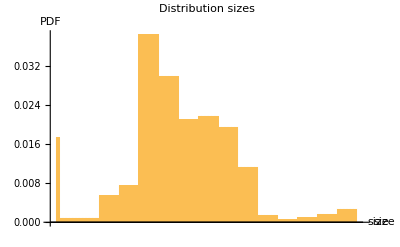
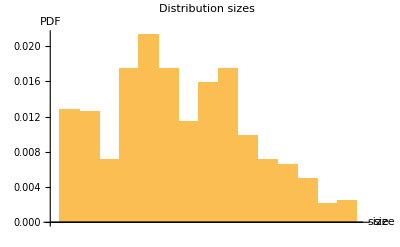
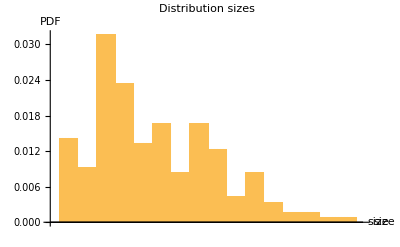
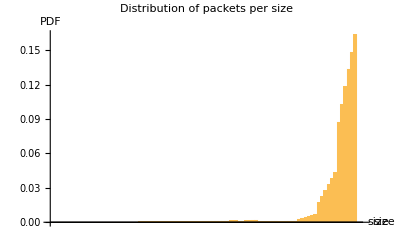
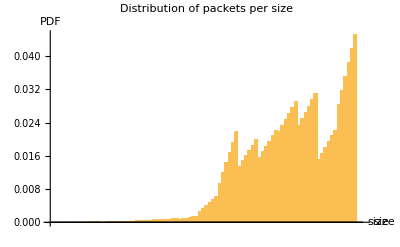
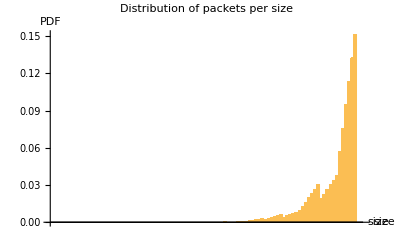
Hadoop | WebSearch | DataMining
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
3.66326×10^6 | 1.55469×10^6 | 5.50755×10^6

```mathematica
distOfSizesHadoop = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesHadoop={distOfSizesHadoop[[1]]}~Join~Table[distOfSizesHadoop[[i]] - distOfSizesHadoop[[i-1]],{i,2,Length[distOfSizesHadoop]}];
sizesHadoop = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]];

distOfSizesDataMining = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesDataMining={distOfSizesDataMining[[1]]}~Join~Table[distOfSizesDataMining[[i]] - distOfSizesDataMining[[i-1]],{i,2,Length[distOfSizesDataMining]}];
sizesDataMining = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","Grid"][[1]][[2;;]][[All,1]];


distOfSizesWebSearch = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesWebSearch={distOfSizesWebSearch[[1]]}~Join~Table[distOfSizesWebSearch[[i]] - distOfSizesWebSearch[[i-1]],{i,2,Length[distOfSizesWebSearch]}];
sizesWebSearch = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv","Grid"][[1]][[2;;]][[All,1]];



Grid[{{"Hadoop","WebSearch","DataMining"},{BarChart[distOfSizesHadoop,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}],BarChart[distOfSizesWebSearch,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}],BarChart[distOfSizesDataMining,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]},{BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}],BarChart[Table[N[(distOfSizesWebSearch[[j]]*sizesWebSearch[[j]] )/Total[Table[distOfSizesWebSearch[[i]]*sizesWebSearch[[i]],{i,1,Length[sizesWebSearch]}]]],{j,1,Length[sizesWebSearch]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}],BarChart[Table[N[(distOfSizesDataMining[[j]]*sizesDataMining[[j]] )/Total[Table[distOfSizesDataMining[[i]]*sizesDataMining[[i]],{i,1,Length[sizesDataMining]}]]],{j,1,Length[sizesDataMining]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]},{Total[Table[sizesHadoop[[i]]*distOfSizesHadoop[[i]],{i,1,Length[sizesHadoop]}]],Total[Table[sizesWebSearch[[i]]*distOfSizesWebSearch[[i]],{i,1,Length[sizesWebSearch]}]],Total[Table[sizesDataMining[[i]]*distOfSizesDataMining[[i]],{i,1,Length[sizesDataMining]}]]}}]


BarChart[distOfSizesHadoop,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];

BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Total[Table[sizesHadoop[[i]]*distOfSizesHadoop[[i]],{i,1,Length[sizesHadoop]}]];
```

Number of flowlets in window:

```mathematica
Subscript[list, 40]={{10,46.44561},{20,90.5256},{30,132.91443914439},{40,173.94772},{50,213.8356},{60,252.74132965319},{70,290.72943647182},{80,327.94616},{90,364.41211412114}};
Subscript[list, 400] ={{10,124.21595},{20,217.72968},{30,295.62550625506},{40,362.92448},{50,422.20425},{60,475.12048481939},{70,522.72411620581},{80,565.85456},{90,605.146}};
Subscript[list, 4000] ={{10,301.60049},{20,413.12056},{30,466.59103591036},{40,494.55032},{50,510.04655},{60,518.95721828873},{70,524.27616380819},{80,527.63152},{90,529.80847808478}};
Subscript[list, 40000] ={{10,140.30559},{20,141.39894},{30,141.91869918699},{40,142.43528},{50,142.95135},{60,143.46573862955},{70,143.98809940497},{80,144.50424},{90,145.0202502025}};

ListPlot[{Callout[Subscript[list, 40],"Mean = 40 M"],Callout[Subscript[list, 400],"Mean = 400 M"],Callout[Subscript[list, 4000],"Mean = 2.5 G"],Callout[Subscript[list, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of flowlets that seen at the window"}]
```

-Graphics-

```mathematica
Subscript[newlist, 40]={{10,4426.63962},{20,4428.44124},{30,4430.2349923499},{40,4432.05148},{50,4433.86395},{60,4435.5899435977},{70,4437.3750787539},{80,4439.26128},{90,4441.0571505715}};
Subscript[newlist, 400] ={{10,1130.41252},{20,1132.442},{30,1134.4671946719},{40,1136.50688},{50,1138.54415},{60,1140.5311412456},{70,1142.5686384319},{80,1144.62856},{90,1146.6562865629}};
Subscript[newlist, 4000] ={{10,530.49309},{20,532.81376},{30,535.14094140941},{40,542.10026401056},{50,539.78855},{60,542.10026401056},{70,544.41575078754},{80,546.75304},{90,549.09144091441}};
Subscript[newlist, 40000] ={{10,142.9596},{20,145.54734},{30,148.13356133561},{40,150.72184},{50,153.30955},{60,155.89523580943},{70,158.48925446272},{80,161.07736},{90,163.66474664747},{1000,424.6548}};

ListPlot[{Callout[Subscript[newlist, 40],"Mean = 40 M"],Callout[Subscript[newlist, 400],"Mean = 400 M"],Callout[Subscript[newlist, 4000],"Mean = 2.5 G"],Callout[Subscript[newlist, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of living flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of living flowlets"}]
```

-Graphics-

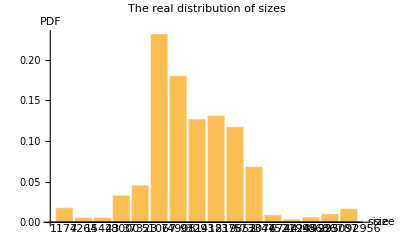

```mathematica
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}]];
plotData[file_,withElephant_,sizes_]:=Module[{str,listStrings,missCount,outOfOrder,sum,l,x},(
str = Import[file];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];
outOfOrder = ToExpression[ StringDrop[listStrings[[2]],{-3}]];



sum = Total[Map[#[[3]]&,missCount]];
data = Map[{#[[1]],100*#[[2]],#[[3]]}&,outOfOrder];
d=Map[Module[{s},s=Floor[#];Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,sizes];
(*The miss count:*)
missCountList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,missCount];
If[withElephant == True,rtt = (5.8)*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt;
missHopPlots = Map[Module[{s,oneSzie,oneSum,oneMean},s=Floor[#];
oneSzie = Select[missCount,(#[[1]]==s)&];
oneSum = Total[Map[#[[3]]&,oneSzie]];
oneMean = N[Total[Map[#[[4]]&,oneSzie]]/oneSum];
Labeled[ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT\nrate = " <> ToString[pivot/10^6] <> " Mbps",Tiny],Automatic]}],"Avg miss hop = " <> ToString[oneMean]]
]&,sizes];
Return[{missHopPlots,N[Total[Map[#[[4]]&,missCount]]/sum]}];

(*Size distribution validation:*)
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}]];
Print[BarChart[N[1/Total[d]*d],ChartLabels->sizes,PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]];
Print[ListPlot3D[missCountList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Miss count",AxesLabel->{"size (Bytes)","rate (Mbps)","miss count"},PlotRange->{0,4}]];
Print["The mean of the miss count: ",N[Total[Map[#[[4]]&,missCount]]/sum]];


Print[missHopPlots];
Print[Total[missHopPlots]];

hashsize[size_]:=Position[sizes,size][[1]][[1]];
heatMap = ConstantArray[0,{17,40000/100}];
Map[((heatMap[[hashsize[#[[1]]],(#[[2]])/100]] = #[[3]]))&,data3];

outOfOrderList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,outOfOrder];
Print[ListPlot3D[outOfOrderList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Out of order",AxesLabel->{"size (Bytes)","rate (Mbps)","out of oreder"},PlotRange->All]];
Print[Map[Module[{s},s=#;ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[outOfOrderList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s],AxesLabel->{"Rate (Mbps)","Avg out of order"}]]&,sizes]];

Print["The mean of the out of oreder: ",N[Total[Map[(#[[4]])/sum&,outOfOrder]]]];
)];

sizeDistributionValidationI[file_,sizes_]:=Module[{str,listStrings,missCount,data,probs,d},(
str = Import[file];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];


data = Map[{#[[1]],100*#[[2]],#[[3]]}&,missCount];
d=Map[Module[{s},s=Floor[#];Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,DeleteDuplicates[data[[All,1]]]];
d = N[1/Total[d]*d];
probs = Switch[sizes,sizesHadoop,distOfSizesHadoop,sizesWebSearch,distOfSizesWebSearch,sizesDataMining,distOfSizesDataMining];
Grid[{{BarChart[Table[Tooltip[probs[[i]],"size = "<>ToString[sizes[[i]]]<>" , p = "<>ToString[probs[[i]]]],{i,Length[probs]}],PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}],BarChart[Table[Tooltip[d[[i]],"size = "<>ToString[sizes[[i]]]<>" , p = "<>ToString[d[[i]]]],{i,Length[d]}],PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]}}])];
missCountAvg[file_]:=Module[{FileAsList,indexOfMissCount},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.dest \"miss count\""][[1]][[1]];
ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 2]]]]])];

getPercentageOfTrafficToController[file_]:=Module[{FileAsList,indexOfMissCount},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.dest \"miss count\""][[1]][[1]];
N[ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 12]]]]]/ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 1]]]]]])];


distributions = {"C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv"};
createDist[dist_]:=Module[{sizes,prob},(
prob = Import[dist,"Grid"][[1]][[2;;]][[All,2]];
prob={prob[[1]]}~Join~Table[prob[[i]] - prob[[i-1]],{i,2,Length[prob]}];
sizes = Import[dist,"Grid"][[1]][[2;;]][[All,1]];
Return[EmpiricalDistribution[prob->sizes]]
)];



plotResults[file_,cacheSizes_,thresholds_]:=Module[{temp,improveBandToCont,improveMissCount,thMinimalMissHop,thMinimalBand},(
Print[ListLogLinearPlot[Outer[(temp={#2,missCountAvg[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]};Tooltip[If[temp[[1]]==0,{thresholds[[2]]/1.2(*Where to show the point of 0*),temp[[2]]},temp],temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]&,cacheSizes],Joined->True,AxesLabel->{"threshold (rate)","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]];
Print[ListLogLinearPlot[Outer[(temp={#2,getPercentageOfTrafficToController[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]};Tooltip[If[temp[[1]]==0,{thresholds[[2]]/1.2(*Where to show the point of 0*),temp[[2]]},temp],temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]&,cacheSizes],Joined->True,AxesLabel->{"threshold (rate)","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]];





Print[Quiet[sizeDistributionValidationI[StringReplace[file,{"AAA"->ToString[cacheSizes[[1]]],"BBB"->ToString[thresholds[[1]]],"scalar-file.sca"->"Total.txt"}],sizesHadoop]]];


temp = Outer[({#2,missCountAvg[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]})&,cacheSizes,thresholds];
thMinimalMissHop =Table[MinimalBy[temp[[i]],Last][[1]][[1]],{i,1,Length[cacheSizes]}] ;
improveMissCount = Table[(1-Min[Transpose[temp[[i]]][[2]]]/Transpose[temp[[i]]][[2]][[1]])*100,{i,1,Length[cacheSizes]}];
temp = Outer[({#2,getPercentageOfTrafficToController[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]})&,cacheSizes,thresholds];
thMinimalBand =Table[MinimalBy[temp[[i]],Last][[1]][[1]],{i,1,Length[cacheSizes]}] ;
improveBandToCont = Table[(1-Min[Transpose[temp[[i]]][[2]]]/Transpose[temp[[i]]][[2]][[1]])*100,{i,1,Length[cacheSizes]}];
Print[Grid[Transpose[{{"cache size"}~Join~cacheSizes,{"Improvement in miss count (in percentages)"}~Join~improveMissCount,{"Optimal threshold by miss hop"}~Join~thMinimalMissHop,{"Improvement in bandwidth to controller (in percentages)"}~Join~improveBandToCont,{"Optimal threshold by bandwidth to controller"}~Join~thMinimalBand}],Frame->All]];
)];
```

With/Without elephant Detector push = 1,2,10:

```mathematica
{q1,nav1} = plotData["with 1,1.txt",True];
{q2,nav2} = plotData["witout 1,1.txt",False];
{q3,nav3} = plotData["with 2,2.txt",True];
{q4,nav4}= plotData["without 2,2.txt",False];
{q5,nav5}= plotData["with 10,10.txt",True];
{q6,nav6}= plotData["without 10,10.txt",False];
Manipulate[{Labeled[q1[[i]],"With 1,1\n Total Avg miss hop = " <> ToString[nav1]],Labeled[q2[[i]],"Without 1,1\n Total Avg miss hop = " <> ToString[nav2]],Labeled[q3[[i]],"With 2,2\n Total Avg miss hop = " <> ToString[nav3]],Labeled[q4[[i]],"Without 2,2\n Total Avg miss hop = " <> ToString[nav4]],Labeled[q5[[i]],"With 10,10\n Total Avg miss hop = " <> ToString[nav5]],Labeled[q6[[i]],"Without 10,10\n Total Avg miss hop = " <> ToString[nav6]]},{i,1,Length[sizes],1}]
```

Set::shape: Lists {q1,nav1} and plotData[with 1,1.txt,True] are not the same shape.

Set::shape: Lists {q2,nav2} and plotData[witout 1,1.txt,False] are not the same shape.

Set::shape: Lists {q3,nav3} and plotData[with 2,2.txt,True] are not the same shape.

Set::shape: Lists {q4,nav4} and plotData[without 2,2.txt,False] are not the same shape.

Set::shape: Lists {q5,nav5} and plotData[with 10,10.txt,True] are not the same shape.

Set::shape: Lists {q6,nav6} and plotData[without 10,10.txt,False] are not the same shape.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Static Ideal Elephant Detector According to size:

```mathematica
Map[(Subscript[b, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull great then " <> ToString[#] <>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True,sizes])&,sizes];
```

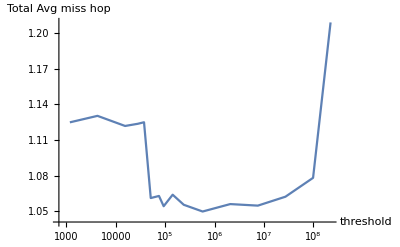

573344

```mathematica
Manipulate[Labeled[Subscript[b, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[b, flowSize][[2]]],Top],{{flowSize,sizes[[1]],"insert a flow whose size is greater than"},sizes}]
ListLogLinearPlot[Map[{#,Subscript[b, #][[2]]}&,sizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[b, #]]&,sizes],Min[Map[Last[Subscript[b, #]]&,sizes]]][[1]][[1]]]]
```

Dynamic Elephant Detector According to Hit Ratio (Local/Total)Threshold =   size:

```mathematica
reset= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\\4.09999999999999964473  -  4.20000000000000017764.txt",True];
nonReset = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\\4.09999999999999964473  -  4.20000000000000017764.txt",True];
```

```mathematica
Manipulate[{Labeled[reset[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[reset[[2]]],Top],Labeled[nonReset[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[nonReset[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]
```

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\4.09999999999999964473  -  4.20000000000000017764.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\4.09999999999999964473  -  4.20000000000000017764.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ToExpression::sntx: Invalid syntax in or before "General-0-20221224-11:30:19-5128".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221224-11:30:19".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "ratio/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

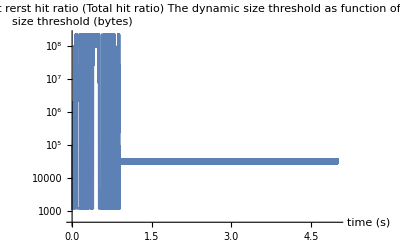

The maximum threshold after 1s is 37323
The minimum threshold after 1s is 28000

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"Without rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221224-11:31:23-18328".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221224-11:31:23".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "ratio/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

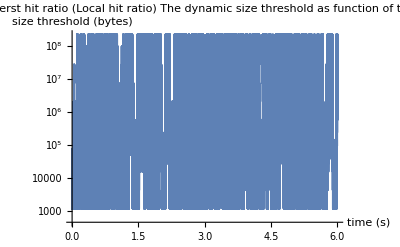

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"With rerst hit ratio (Local hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-08:39:09-12308".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-08:39:09".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

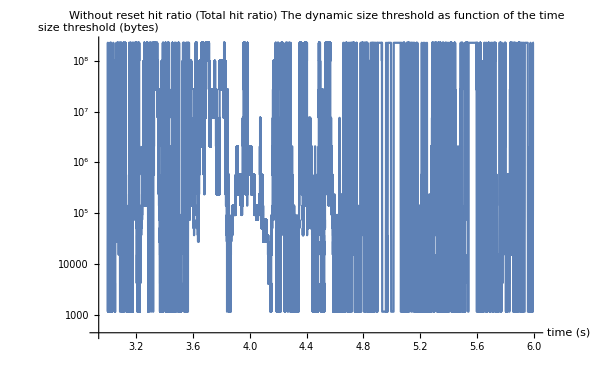

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-08:39:44-8252".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-08:39:44".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

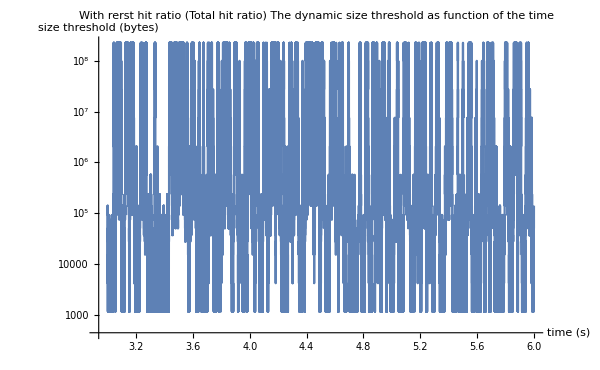

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf dynamic non reset\5.50000000000000000000  -  6.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf dynamic with reset\5.50000000000000000000  -  6.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
reset1= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic non reset\\5.50000000000000000000  -  6.00000000000000000000.txt",True];
nonReset1 = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic with reset\\5.50000000000000000000  -  6.00000000000000000000.txt",True];
Manipulate[{Labeled[reset1[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[reset1[[2]]],Top],Labeled[nonReset1[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[nonReset1[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]

s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"Without reset hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]


s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"With rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

Static Ideal Elephant Detector According to Log(Size * Rate):

```mathematica
Map[(Subscript[bb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 log pull = "<>ToString[#]<>", push = inf,inf\\3.50000000000000000000  -  4.00000000000000000000.txt",True])&,Range[30,42,1]];
Print[""]
```

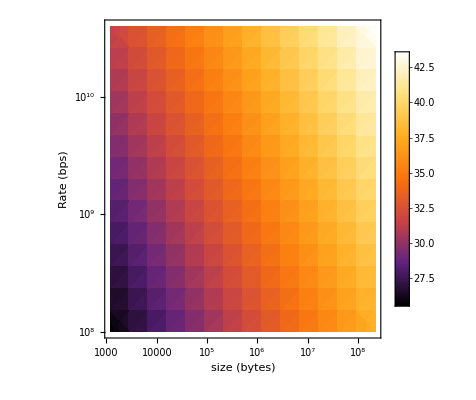

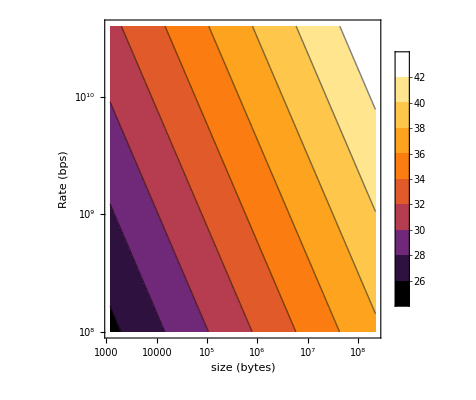

```mathematica
DensityPlot[Log[x r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[x r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

```mathematica
Manipulate[Labeled[Subscript[bb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bb, flowSize][[2]]],Top],{{flowSize,Range[30,42,1][[1]],"insert a flow whose size is greater than"},Range[30,42,1]}]
ListLogLinearPlot[Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
Range[30,42,1][[Position[Map[Last[Subscript[bb, #]]&,Range[30,42,1]],Min[Map[Last[Subscript[bb, #]]&,Range[30,42,1]]]][[1]][[1]]]]
```

-Graphics-

30

Dynamic Threshold Log(Size * Rate):

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-19:10:38-10624".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-19:10:38".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

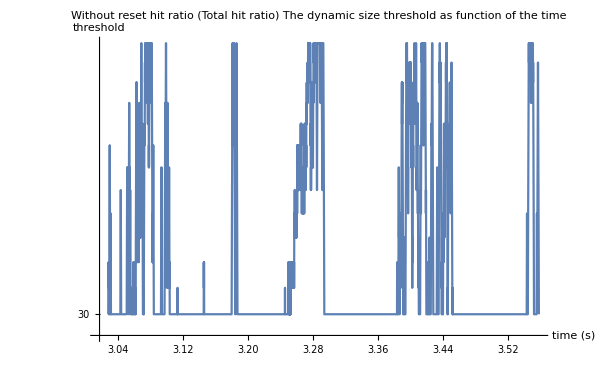

The maximum threshold after 1s is 42
The minimum threshold after 1s is 30

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-19:11:18-12436".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-19:11:18".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

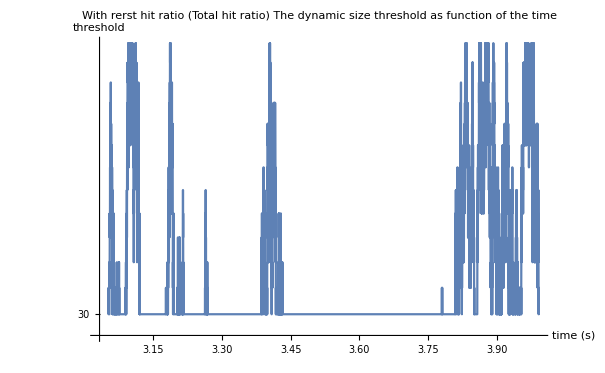

The maximum threshold after 1s is 42
The minimum threshold after 1s is 30

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\3.50000000000000000000  -  4.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\3.50000000000000000000  -  4.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
logreset= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\\3.50000000000000000000  -  4.00000000000000000000.txt",True];
lognonreset = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\\3.50000000000000000000  -  4.00000000000000000000.txt",True];
Manipulate[{Labeled[logreset[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[logreset[[2]]],Top],Labeled[lognonreset[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[lognonreset[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]

s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[30,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"},PlotLabel->"Without reset hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]


s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[30,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"},PlotLabel->"With rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

Static Ideal Push Algorithm According to size:

```mathematica
Map[(Subscript[c, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 without pull push = "<>ToString[#]<>" flow size\\3.50000000000000000000  -  4.00000000000000000000.txt",False,sizes])&,sizes[[6;;]]];
```

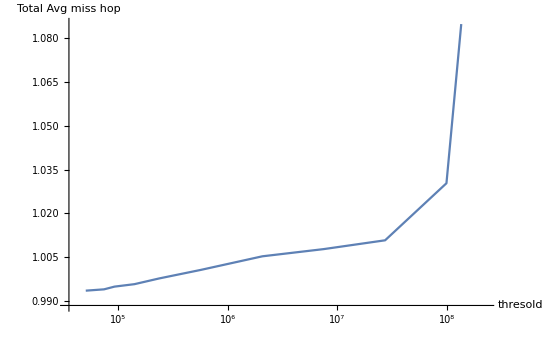

51067

```mathematica
Manipulate[Labeled[Subscript[c, flowSize][[1]],"without pull,insert all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[c, flowSize][[2]]],Top],{{flowSize,sizes[[6]],"insert a flow whose size is greater than"},sizes[[6;;]]}]
ListLogLinearPlot[Map[{#,Subscript[c, #][[2]]}&,sizes[[6;;]]],Joined->True,AxesLabel->{"thresold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[c, #]]&,sizes[[6;;]]],Min[Map[Last[Subscript[c, #]]&,sizes[[6;;]]]]][[1]][[1]]+ 5]]
```

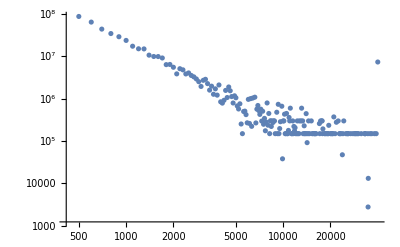

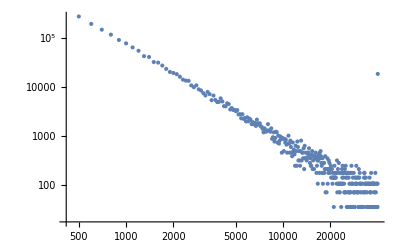

-Graphics-

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==223092956)&]],PlotRange->All]
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==51067)&]],PlotRange->All]

ListLogLogPlot[Map[Module[{x},x=#;Callout[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==x)&]],x]]&,sizes],PlotRange->All,Joined->True]
```

```mathematica
Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]]
lognonreset[[2]]
logreset[[2]]
```

{{30,True},{31,True},{32,True},{33,True},{34,True},{35,True},{36,True},{37,True},{38,True},{39,True},{40,True},{41,True},{42,True}}

True

True

```mathematica
Row[-Graphics-,-Graphics-]
```

Row[-Graphics-,-Graphics-]

-Graphics-

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate) = 39\\3.94999999999999973355  -  4.00000000000000000000.txt",True]
```

plotData[C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate) = 39\3.94999999999999973355  -  4.00000000000000000000.txt,True]

```mathematica
Range[26,42,1]
```

{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

Static Ideal Elephant Detector According to Size:

```mathematica
Map[(Subscript[bbbb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new static size\\2.5 G cache = 1000 push = inf elephant or pull size greater than "<>ToString[#]<>" final\\4.50000000000000000000  -  5.00000000000000000000.txt",True])&,sizes];
Print[""]
Manipulate[Labeled[Subscript[bbbb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bbbb, flowSize][[2]]],Top],{{flowSize,Range[26,42,1][[1]],"insert a flow whose size is greater than"},sizes}]
ListLogLinearPlot[Map[{#,Subscript[bbbb, #][[2]]}&,sizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[bbbb, #]]&,sizes],Min[Map[Last[Subscript[bbbb, #]]&,sizes]]][[1]][[1]]]]
```

-Graphics-

1177

Static Ideal Elephant Detector According to Log(Size * Rate):

```mathematica
DensityPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

-Graphics-

-Graphics-

```mathematica
Map[(Subscript[bbb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G cache = 1000 push = inf elephant or pull LOG(size Rate) greater than "<>ToString[#]<>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True])&,Range[26,42,1]];
Print[""]
Manipulate[Labeled[Subscript[bbb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bbb, flowSize][[2]]],Top],{{flowSize,Range[26,42,1][[1]],"insert a flow whose size is greater than"},Range[26,42,1]}]
Row[{ListLogLinearPlot[Map[{#,Subscript[bbb, #][[2]]}&,Range[26,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}],ListLogLinearPlot[Map[{#,Subscript[bbb, #][[2]]}&,Range[26,39,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]}]
Range[26,42,1][[Position[Map[Last[Subscript[bbb, #]]&,Range[26,42,1]],Min[Map[Last[Subscript[bbb, #]]&,Range[26,42,1]]]][[1]][[1]]]]
```

-Graphics--Graphics-

26

Dynamic Elephant Detector According to Hit Ratio (Local/Total):

```mathematica
resetLog =   plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
nonresetLog = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
resetSize =  plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size with reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
nonresetSize =  plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size non reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];

Manipulate[Grid[{{Labeled[resetLog[[1]][[i]],"Threshold log(size * rate)learning with reset hit ratio\n Total Avg miss hop = " <> ToString[resetLog[[2]]],Top],plot1},
{Labeled[nonresetLog[[1]][[i]],"Threshold log(size * rate) learning without reset hit ratio\n Total Avg miss hop = " <> ToString[nonresetLog[[2]]],Top],plot2},
{Labeled[resetSize[[1]][[i]],"Threshold size learning with reset hit ratio\n Total Avg miss hop = " <> ToString[resetSize[[2]]],Top],plot3},
{Labeled[nonresetSize[[1]][[i]],"Threshold size learning without reset hit ratio\n Total Avg miss hop = " <> ToString[nonresetSize[[2]]],Top],plot4}}],{{i,1,"flow size index"},1,16,1}]
```

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-20:11:37-15580".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-20:11:37".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

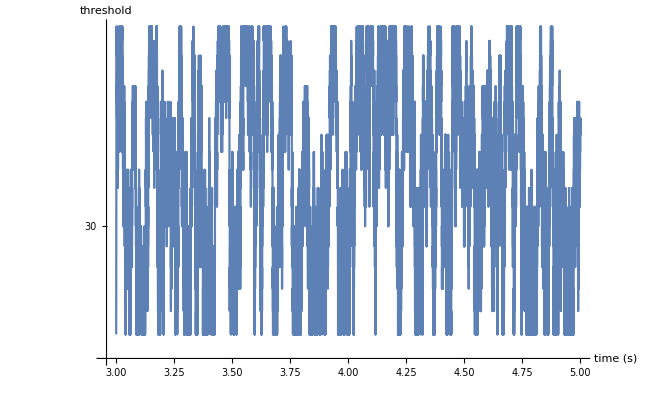

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[25,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot1 = ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-20:11:56-8688".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-20:11:56".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

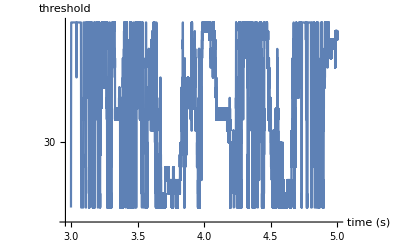

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[25,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot2= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-19:43:28-16708".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-19:43:28".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

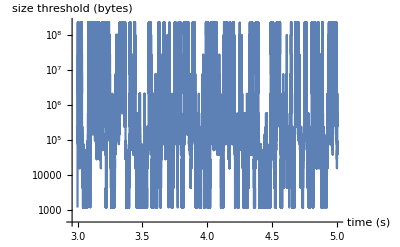

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot3= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-19:43:54-13840".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-19:43:54".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

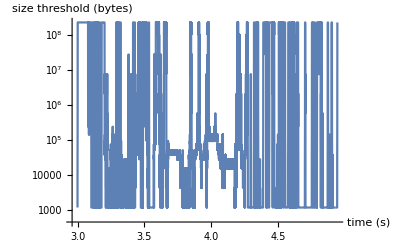

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot4= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"}]
```

```mathematica
Grid
```

Grid

```mathematica
resetLog===nonresetLog
```

False

```mathematica
Range[26,42,1]
```

{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

```mathematica
Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]]
```

{1177,1691.5,2206,2720.5,3235,3749.5,4264,6127.17,7990.33,9853.5,11716.7,13579.8,15443,17535.8,19628.7,21721.5,23814.3,25907.2,28000,29553.8,31107.7,32661.5,34215.3,35769.2,37323,39613.7,41904.3,44195,46485.7,48776.3,51067,55040.5,59014,62987.5,66961,70934.5,74908,77972.2,81036.3,84100.5,87164.7,90228.8,93293,101381.,109468.,117556,125644.,133731.,141819,157825.,173830.,189836,205842.,221847.,237853,293768.,349683.,405599.,461514.,517429.,573344,823911.,1070000,1330000,1580000,1830000,2076744,2980000,3890000,4800000,5710000,6610000,7521945,10800000,14100000,17400000,20700000,24000000,27244995,39200000,51100000,63000000,74900000,86800000,98686787,119000000,140000000,161000000,182000000,202000000,223092956}

Static Ideal Elephant Detector According to Log(Size * Rate):

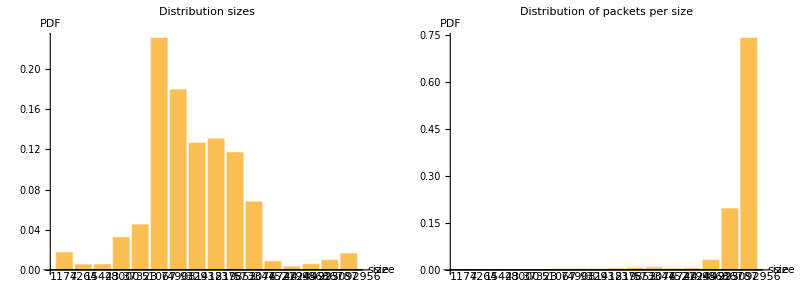

```mathematica
Subscript[a, 1] = BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];
Subscript[a, 2]=BarChart[Table[N[(distOfSizes[[j]]*sizes[[j]])/Total[Table[distOfSizes[[i]]*sizes[[i]],{i,1,16}]]],{j,1,16}],ChartLabels->sizes,PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Grid[{{Subscript[a, 1],Subscript[a, 2]}}]
```

Static Ideal Elephant Detector According to Log(Size * Rate):

DensityPlot::exclul: {Im[ⅇ^(Charting`Private`pvar$51496) result$51504]-0} must be a list of equalities or real-valued functions.

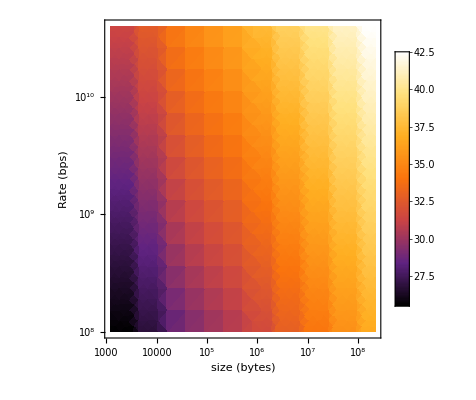

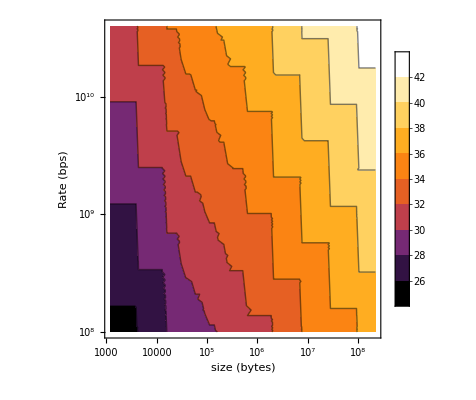

```mathematica
f[x_]:=Module[{result},Table[If[x ≤ sizes[[i]] && x ≥ sizes[[i-1]],result = sizes[[i-1]] ],{i,2,Length[sizes]}];result];
DensityPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

```mathematica
Map[(Subscript[bb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 log pull = "<>ToString[#]<>", push = inf,inf\\3.50000000000000000000  -  4.00000000000000000000.txt",True])&,Range[30,42,1]];
Manipulate[Labeled[Subscript[bb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bb, flowSize][[2]]],Top],{{flowSize,Range[30,42,1][[1]],"insert a flow whose size is greater than"},Range[30,42,1]}]
ListLogLinearPlot[Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
Range[30,42,1][[Position[Map[Last[Subscript[bb, #]]&,Range[30,42,1]],Min[Map[Last[Subscript[bb, #]]&,Range[30,42,1]]]][[1]][[1]]]]
```

-Graphics-

30

BarChart::ldata: True/Total[True] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[True/Total[True],ChartLabels→True,PlotLabel→Distribution of sizes in the simulation,AxesLabel→{size,PDF}]

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

BarChart[True/Total[True],ChartLabels→True,PlotLabel→Distribution of sizes in the simulation,AxesLabel→{size,PDF}]

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

The new distribution of the sizes:

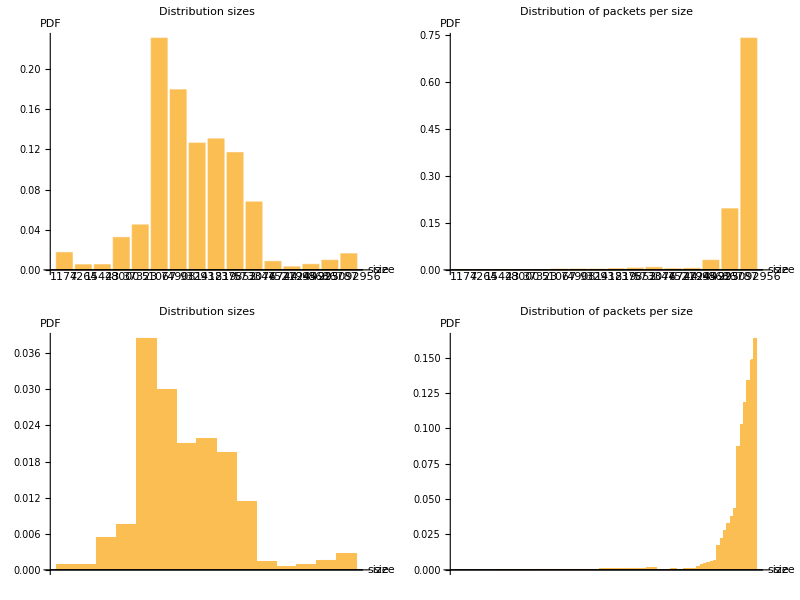

```mathematica
newdistOfSizes = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
Subscript[a, 3]:=BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];

Subscript[a, 4]:=BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Total[Table[sizes[[i]]*distOfSizes[[i]],{i,1,Length[sizes]}]];
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]];

Grid[{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}}]
```

```mathematica
Map[(Subscript[b, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull great then " <> ToString[#] <>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True,sizes])&,sizes];
```

```mathematica
plotData["C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with quantile cache=1000\2.5 G cache=1000 push in cont_swt=117556,push in agg_swt=117556\13.00000000000000000000-14.00000000000000000000.txt",True,sizes]
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with quantile cache=1000\2.5 G cache=1000 push in cont_swt=117556,push in agg_swt=117556\13.00000000000000000000-14.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72302&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$72302& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$72302& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72302&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72391&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

{{-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.},1.}

####################################################################################################################################################

```mathematica
ff[cnt_,agg_,chooseSize_]:=(
str = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with quantile cache = 1000\\2.5 G cache = 1000 push in cont_swt = "<>ToString[cnt]<>",push in agg_swt = "<>ToString[agg]<>"\\13.00000000000000000000  -  14.00000000000000000000.txt"];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];
sum = Total[Map[#[[3]]&,missCount]];
data = Map[{#[[1]],100*#[[2]],#[[3]]}&,missCount];

(*The miss count:*)
missCountList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,missCount];
If[True == True,rtt = (5.8)*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt;
return = Module[{s,oneSzie,oneSum,oneMean},s=Floor[chooseSize];
oneSzie = Select[missCount,(#[[1]]==s)&];
oneSum = Total[Map[#[[3]]&,oneSzie]];
oneMean = N[Total[Map[#[[4]]&,oneSzie]]/oneSum];
Labeled[ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT\nrate = " <> ToString[pivot/10^6] <> " Mbps",Tiny],Automatic]}],"Avg miss hop = " <> ToString[oneMean]]
];
Return[{return,N[Total[Map[#[[4]]&,missCount]]/sum]}]);
```

```mathematica
117556
```

117556

```mathematica
ff[117556,117556,1070000]
ff[117556,117556,90228.8]
```

{-Graphics-Avg miss hop = 0.973705,0.93399}

{-Graphics-Avg miss hop = 2.51826,0.93399}

```mathematica
quantiles = {37323,44195,51067,62987.5,74908,90228.8,117556,173830,293768,223092956};
```

```mathematica
Map[{#,ff[#,#,1070000][[2]]}&,quantiles]
```

{{37323,0.935804},{44195,0.94063},{51067,0.939488},{62987.5,0.949062},{74908,0.9342},{90228.8,0.94843},{117556,0.93399},{173830,0.955235},{293768,0.938795},{223092956,2.21813}}

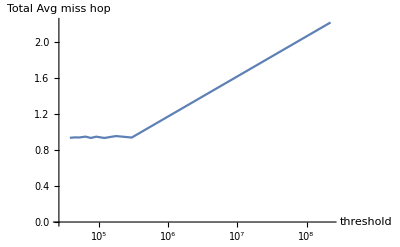

```mathematica
ListLogLinearPlot[Map[{#,ff[#,#,1070000][[2]]}&,quantiles],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

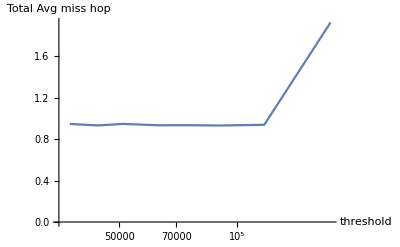

```mathematica
ListLogLinearPlot[Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

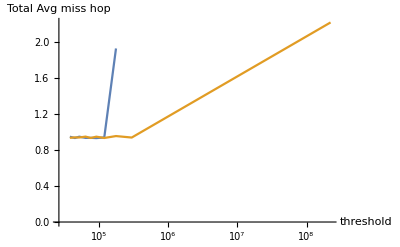
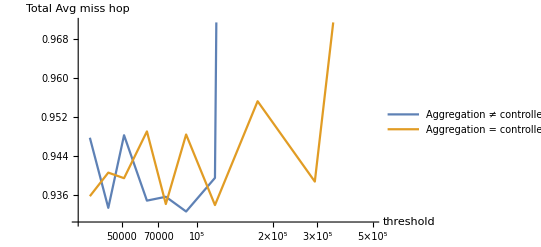
-Graphics- | -Graphics-

```mathematica
aaa = ListLogLinearPlot[{Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Map[{#,ff[#,#,1070000][[2]]}&,quantiles]},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All];
bbb = ListLogLinearPlot[{Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Map[{#,ff[#,#,1070000][[2]]}&,quantiles]},PlotLegends->{"Aggregation ≠ controllerswitch","Aggregation = controllerswitch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{{0,500000},Automatic}];
Grid[{{aaa,bbb}}]
```

```mathematica
Table[ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]],{i,1,Length[quantiles]-2}]
```

{0.947765,0.933417,0.948281,0.934899,0.935688,0.932673,0.939548,1.92883}

```mathematica
Manipulate[Quiet[Module[{x},x=ff[cnt,agg,chooseSize];Grid[{{x[[1]],"Total Avg miss count = "<> ToString[x[[2]]]}}]]],{{cnt,quantiles[[1]],"The threshold in the controller switch"},quantiles},{{agg,quantiles[[1]],"The threshold in the aggregation switch"},quantiles},{{chooseSize,newsizes[[1]],"The size we observe"},newsizes}]
```

The new distribution of the sizes:

-Graphics-

```mathematica
Manipulate[Quiet[Module[{x},x=ff[cnt,agg,chooseSize];Grid[{{x[[1]],"Total Avg miss count = "<> ToString[x[[2]]]}}]]],{{cnt,quantiles[[1]],"The threshold in the controller switch"},quantiles},{{agg,quantiles[[1]],"The threshold in the aggregation switch"},quantiles},{{chooseSize,newsizes[[1]],"The size we observe"},newsizes}]
```

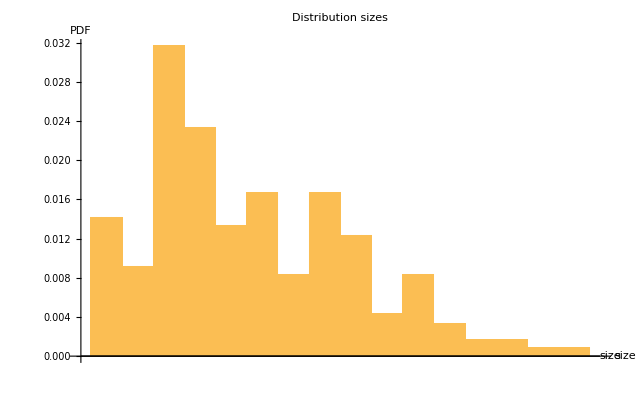

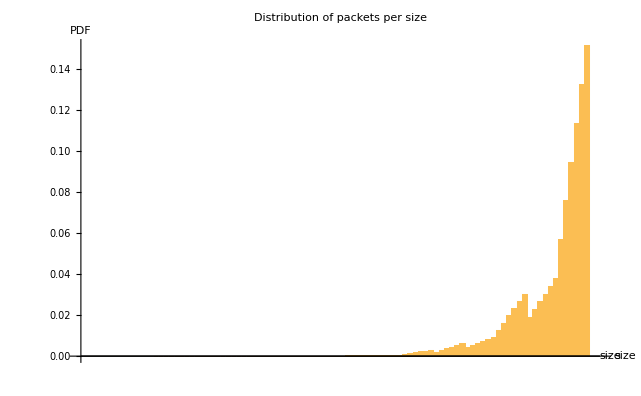

5.50755×10^6

```mathematica
newdistOfSizes = Import["C:\\Users\\0wner\\Downloads\\i-datamining.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\Users\\0wner\\Downloads\\i-datamining.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]

BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]]
```

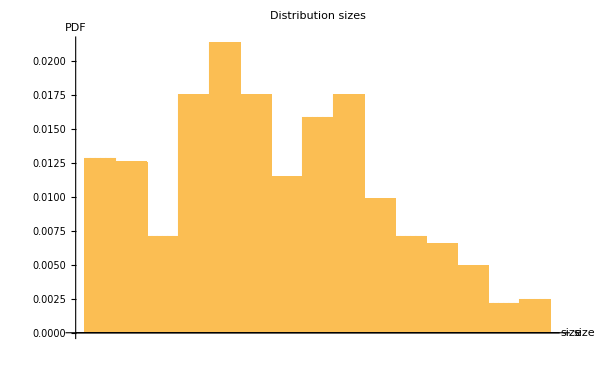

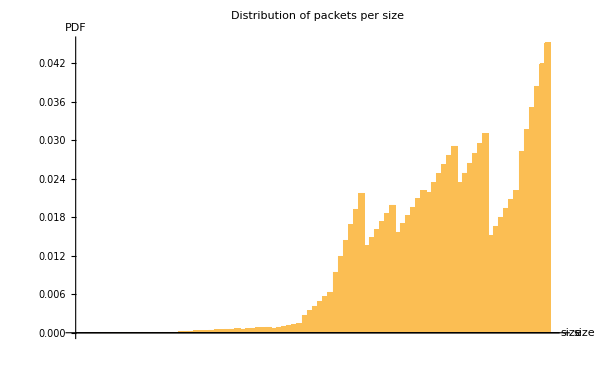

4.866×10^6

1.55469×10^6

```mathematica
newdistOfSizes = Import["C:\\Users\\0wner\\Downloads\\i-websearch.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\Users\\0wner\\Downloads\\i-websearch.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]

BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
Total[Table[sizes[[i]]*distOfSizes[[i]],{i,1,Length[sizes]}]]
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

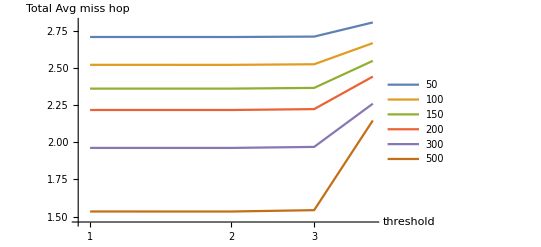

```mathematica
ListLogLinearPlot[Map[Module[{x},x=#;Map[plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[x]<>" push in cont_swt,agg_swt = "<>ToString[#]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]&,{1177,28000,27244995,223092956}]]&,{50,100,150,200,300,500}],PlotLegends->{50,100,150,200,300,500},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

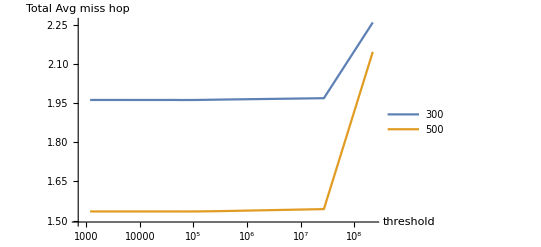

```mathematica
ListLogLinearPlot[Map[Module[{x},x=#;Map[{#,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[x]<>" push in cont_swt,agg_swt = "<>ToString[#]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{1177,28000,37323,51067,62987.5,74908,90228.8,117556,293768,27244995,223092956}]]&,{300,500}],PlotLegends->{300,500},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

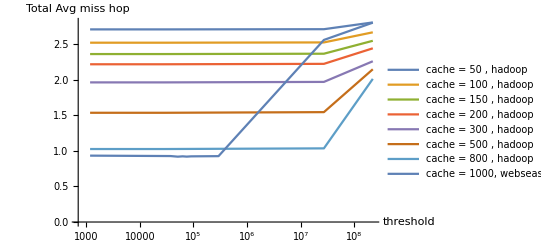

| 1177 | 28000 | 27244995 | 223092956
50 | 2.70663 | 2.70643 | 2.70922 | 2.8043
100 | 2.5196 | 2.51949 | 2.52347 | 2.66551
150 | 2.36002 | 2.36001 | 2.36475 | 2.54642
200 | 2.21643 | 2.21646 | 2.22231 | 2.44065
300 | 1.96187 | 1.96182 | 1.96862 | 2.25874
500 | 1.5349 | 1.53484 | 1.54386 | 2.14616
800 | 1.02559 | 1.02549 | 1.03478 | 2.01111

```mathematica
x=Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{50,100,150,200,300,500,800},{1177,28000,27244995,223092956}];
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,37323,51067,62987.5,74908,90228.8,117556,293768,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

```mathematica
{{"", 1177, 28000, 27244995, 223092956}, {50, 2.7066305282255563, 2.7064303666126994, 2.7092191268121826, 2.8043034923533683}, {100, 2.5196015565490786, 2.519487487786739, 2.523466170767454, 2.665510283363781}, {150, 2.3600185841333823, 2.3600139744590796, 2.3647508500004224, 2.5464178464436173}, {200, 2.2164271494775885, 2.216457922772359, 2.2223106338710323, 2.4406491094435}, {300, 1.961869639209376, 1.9618204029848043, 1.9686245016508455, 2.258738331986653}, {500, 1.5349034781249793, 1.534840644511449, 1.5438629958351842, 2.146162895955437}, {800, 1.0255888887383415, 1.0254861415554506, 1.0347786757586377, 2.011109921346558}}
```

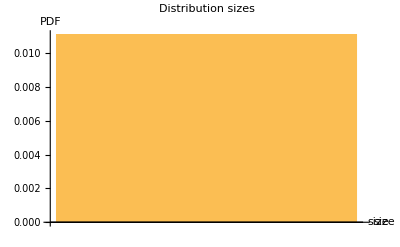

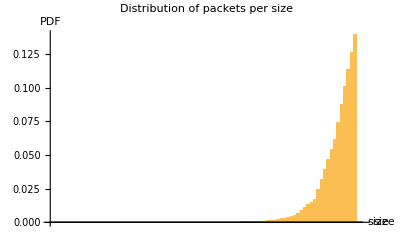

```mathematica
BarChart[ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length],PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]
BarChart[Table[N[(ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length][[j]]*sizesHadoop[[j]])/Total[Table[ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length][[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
```

```mathematica
(*{1177,28000,37323,51067,62987.5,117556,27244995,223092956}*)
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with different cache sizes i websearch\2.5 G cache = 1000 push in cont_swt,agg_swt = 28000\10.50000000000000000000  -  11.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$2241847& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$2241847& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241934&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

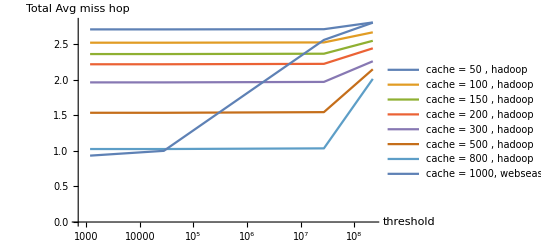

Transpose::nmtx: The first two levels of {{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},«4»,{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Grid[Transpose[Join[{{,50,100,150,200,300,500,800}},Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},{2.5196,2.51949,2.52347,2.66551},{2.36002,2.36001,2.36475,2.54642},{2.21643,2.21646,2.22231,2.44065},{1.96187,1.96182,1.96862,2.25874},{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}}]]],Frame→All,Background→{{1→RGBColor[1, 1, 0]},{1→RGBColor[1, 1, 0]}}]

```mathematica
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,28000,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

```mathematica
x=Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{50,100,150,200,300,500,800},{1177,28000,27244995,223092956}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
x
```

{{{1177,2.70663},{28000,2.70643},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.70922},{223092956,2.8043}},{{1177,2.5196},{28000,2.51949},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.52347},{223092956,2.66551}},{{1177,2.36002},{28000,2.36001},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.36475},{223092956,2.54642}},{{1177,2.21643},{28000,2.21646},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.22231},{223092956,2.44065}},{{1177,1.96187},{28000,1.96182},{37323,1.96192},{51067,1.96174},{62987.5,1.96156},{117556,1.96188},{27244995,1.96862},{223092956,2.25874}},{{1177,1.5349},{28000,1.53484},{37323,1.53478},{51067,1.53492},{62987.5,1.53467},{117556,1.53497},{27244995,1.54386},{223092956,2.14616}},{{1177,1.02559},{28000,1.02549},{37323,1.0252},{51067,1.02502},{62987.5,1.02481},{117556,1.02525},{27244995,1.03478},{223092956,2.01111}}}

```mathematica
Apply[Join,Apply[Join,Outer[{#1,#2,#3}&,{1,2},{3,4},{5,6,7}]]]
```

{{1,3,5},{1,3,6},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,6},{2,4,7}}

```mathematica
sizesDataMining//Length
sizesHadoop//Length
sizesWebSearch//Length
ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length]
```

96

90

90

{1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90}

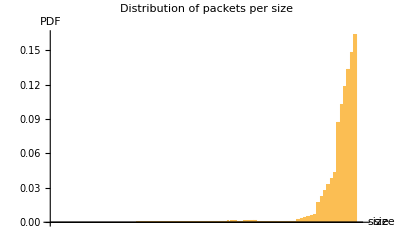

```mathematica
BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
```

```mathematica
(Select[RandomInteger[100,10000000],(#==100)&]//Length)/10000000//N
```

0.0099234

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 150000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 15000000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.38484

2.20937

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 150000\\7.00000000000000000000  -  7.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 15000000\\7.00000000000000000000  -  7.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.38491

2.20917

```mathematica
97121912 - 9510344
```

87611568

```mathematica
2.3848407478945837/2.2093706513635594
```

1.07942

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 1 t = 150000\\5.50000000000000000000  -  6.00000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 1 t = 15000000\\5.50000000000000000000  -  6.00000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

3.

3.

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 2 t = 150000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 2 t = 15000000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.59824

2.40818

```mathematica
StringLength["my_results/The new results/"]
```

27

```mathematica
StringDelete[StringRiffle[ConstantArray["a",27]]," "]
```

aaaaaaaaaaaaaaaaaaaaaaaaaaa

```mathematica
1600000000000/10^12//N
```

1.6

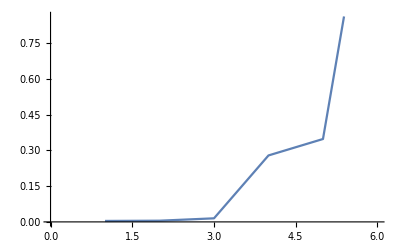

```mathematica
ListPlot[{0.004,0.005,0.01499,0.279,0.348,1.68},Joined->True]
```

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"50% of the traffic is App A and 50% is App B",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

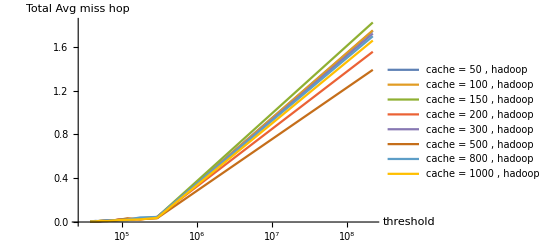

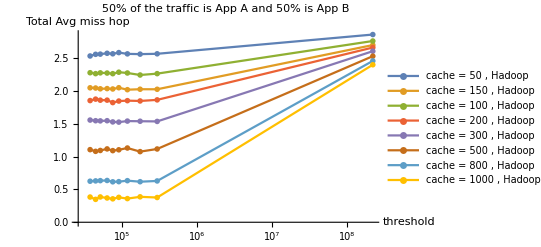

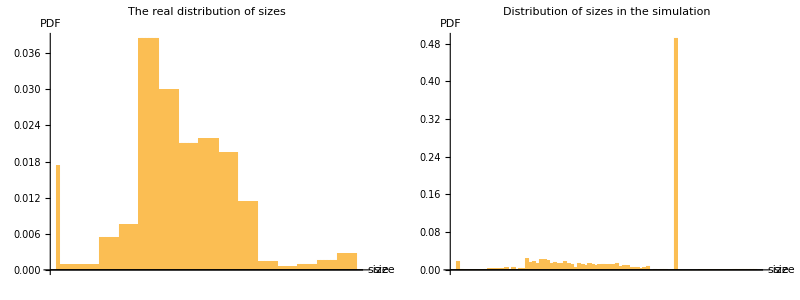

```mathematica
plotgraph[2.5,1.6 *10^12,{50,100,150,200,300,500,800,1000},{37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956},"hadoop"]
```

```mathematica
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,28000,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with different cache sizes i websearch\2.5 G cache = 1000 push in cont_swt,agg_swt = 28000\10.50000000000000000000  -  11.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$2241847& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$2241847& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241934&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

-Graphics-

Transpose::nmtx: The first two levels of {{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},«4»,{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Grid[Transpose[Join[{{,50,100,150,200,300,500,800}},Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},{2.5196,2.51949,2.52347,2.66551},{2.36002,2.36001,2.36475,2.54642},{2.21643,2.21646,2.22231,2.44065},{1.96187,1.96182,1.96862,2.25874},{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}}]]],Frame→All,Background→{{1→RGBColor[1, 1, 0]},{1→RGBColor[1, 1, 0]}}]

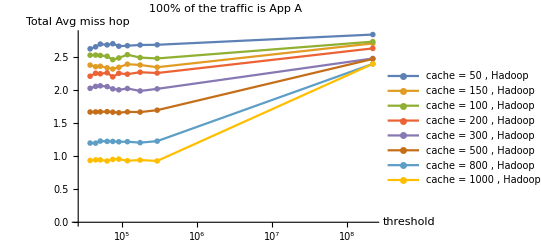

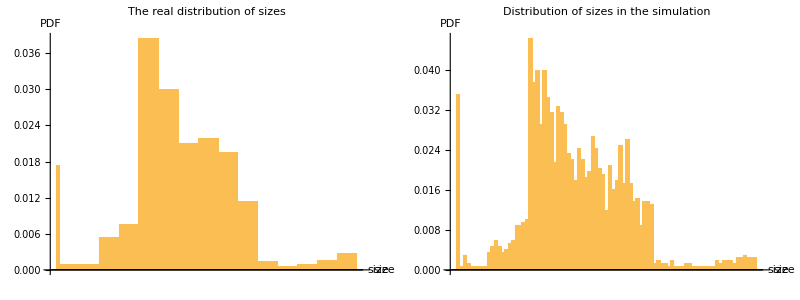

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results with old hosts\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"100% of the traffic is App A",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results with old hosts\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"50% of the traffic is App A and 50% is App B",PlotMarkers->"OpenMarkers"]
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

-Graphics-

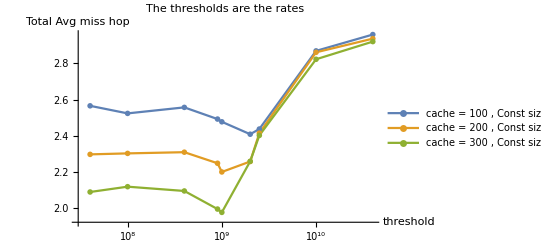

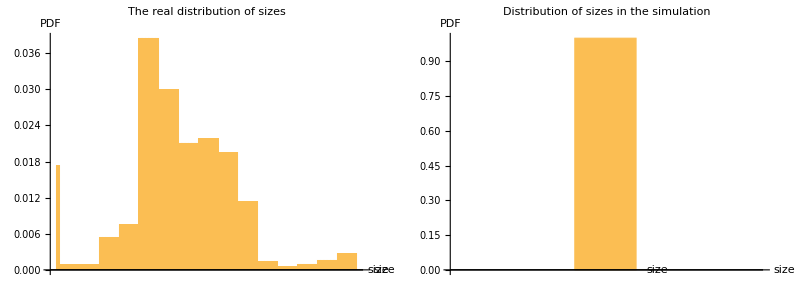

```mathematica
sizeDistribution = "Const size = 4M B";
cacheSizes = {100,200,300};
thresholds = Sort[{2500000000,40000000000,40000000,400000000,100000000,900000000,1000000000,2000000000,10000000000}];
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\ccc rate\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\ccc rate\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 300 push threasholds = 2500000000\\Total.txt",sizesHadoop]
```

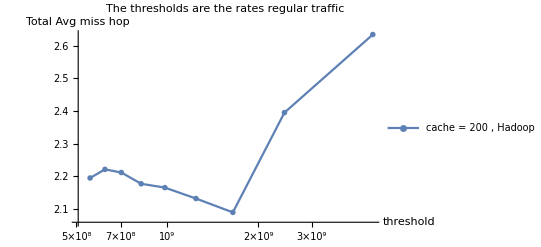

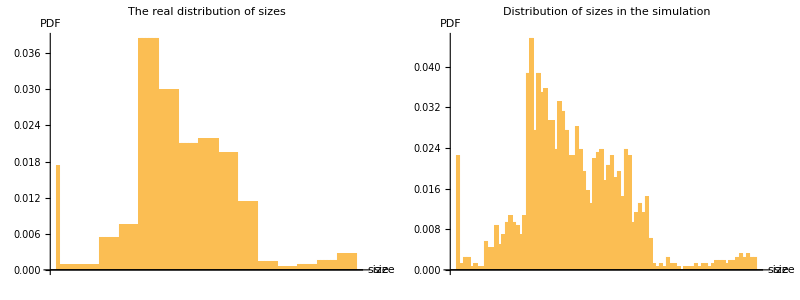

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {200};
thresholds = Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates regular traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 200 push threasholds = 621504292\\Total.txt",sizesHadoop]
```

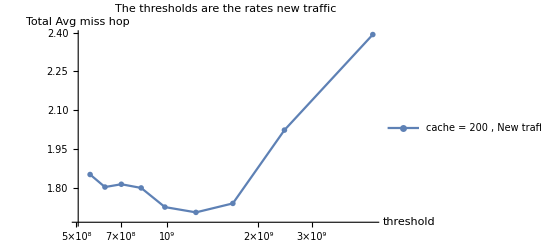

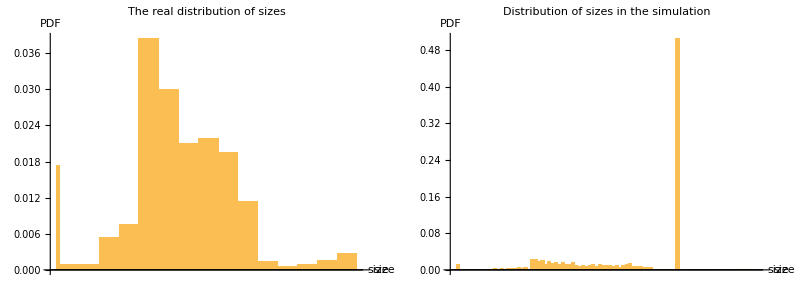

```mathematica
sizeDistribution = "New traffic";
cacheSizes = {200};
thresholds = Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate new hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate new hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 200 push threasholds = 621504292\\Total.txt",sizesHadoop]
```

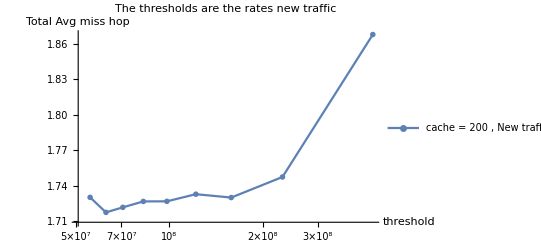

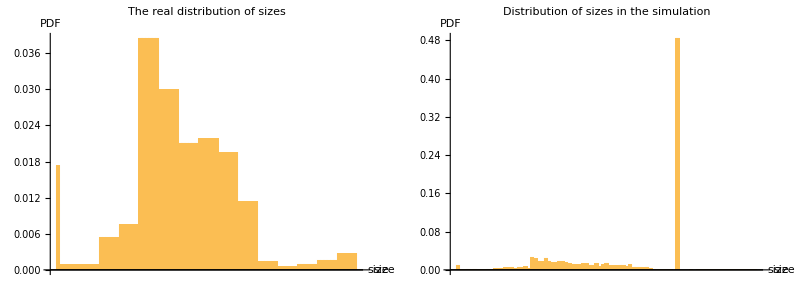

```mathematica
sizeDistribution = "New traffic";
cacheSizes = {200};
thresholds = Sort[{55658062,62593416,70927071,82556950,98284489,121805866,158245781,231309663,451566338}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 15.006s rate = 400M const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = 200 push threasholds = 70927071\\Total.txt",sizesHadoop]
```

Types of applications:

```mathematica
{{"Type", "Description of the Application"}, {"Application A", "The sizes of app A are drawn from i-Hadoop distribution and the destination is drawn from a large Range"}, {"Application B(x)", "The sizes of app B(x) are constant and equal to x and the destination is drawn from a small Range"}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}}
```

Type | Description of the Application
Application A | The sizes of app A are drawn from i-Hadoop distribution and the destination is drawn from a large Range
Application B(x) | The sizes of app B(x) are constant and equal to x and the destination is drawn from a small Range
 | 
 | 
 | 
 | 
 | 
 | 
 |

Types of traffic:

```mathematica
{{"Type", "Description of the traffic"}, {"Traffic A", "All flows is from App A"}, {"Traffic B", "The flows are from app A with a probability of 1/2 and from app B(Avg(Hadoop)) with a probability of 1/2"}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}}
```

Type | Description of the traffic
Traffic A | All flows is from App A
Traffic B | The flows are from app A with a probability of 1/2 and from app B(Avg(Hadoop)) with a probability of 1/2
 | 
 | 
 | 
 | 
 | 
 | 
 |

Benchmark: Push Fast Cache on Traffic B

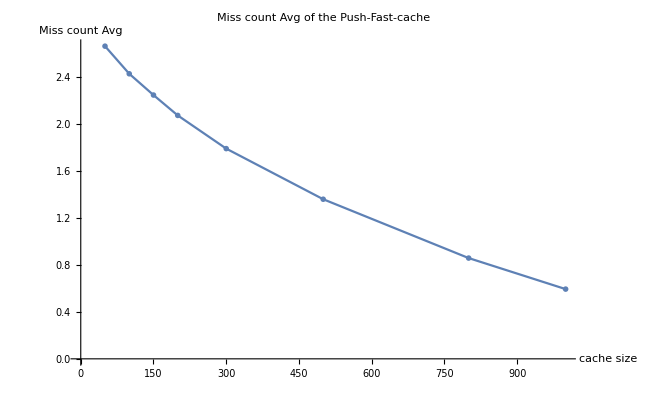

```mathematica
pushFastCacheList = Map[{#,missCountAvg[StringReplace["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{"AAA"->ToString[#],"BBB"->ToString[0]}]]}&,{50,100,150,200,300,500,800,1000}];
ListPlot[Map[Tooltip[#,#]&,pushFastCacheList],Joined->True,PlotMarkers->"OpenMarkers",PlotLabel->"Miss count Avg of the Push-Fast-cache",AxesLabel->{"cache size","Miss count Avg"}]
```

Rates: 2.5G Avg      Traffic: Traffic B

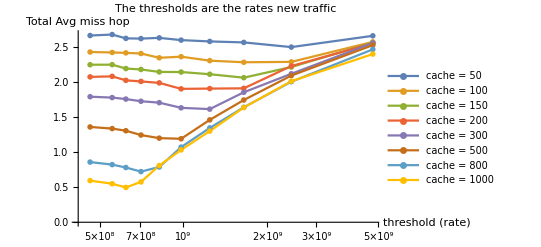

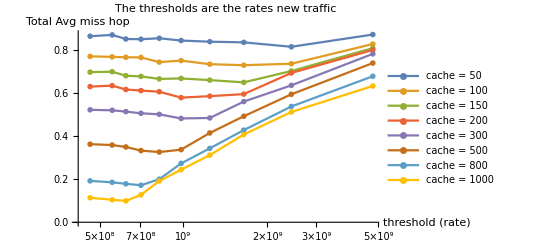

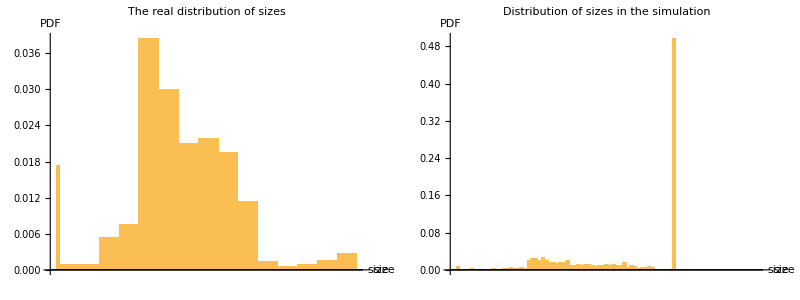

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
50 | 6.19965 | 2437615808 | 5.68238 | 2437615808
100 | 6.01866 | 1645830947 | 5.32464 | 1645830947
150 | 8.22908 | 1645830947 | 6.81979 | 1645830947
200 | 8.23435 | 980967951 | 8.12497 | 980967951
300 | 9.88298 | 1242635857 | 7.6955 | 980967951
500 | 12.4222 | 980967951 | 10.0647 | 818901538
800 | 15.8301 | 704099360 | 10.563 | 704099360
1000 | 16.3723 | 621504292 | 12.8914 | 621504292

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

```mathematica
1500*8*70/((1500*8*10)/555037325)
```

3885261275

Rate Estimator 1: (port-destination) Rate estimator in each switch Rates: 2.5G Avg      Traffic: Traffic B

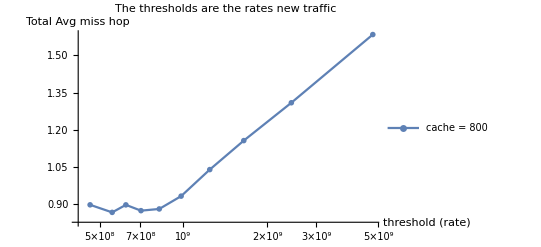

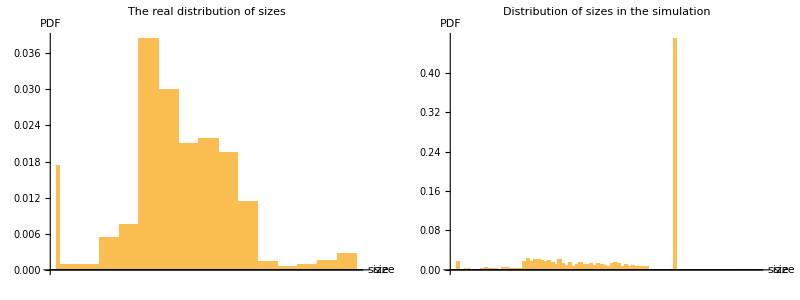

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
800 | 3.41446 | 4.80506

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\port-dest-esti\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rate Estimator 2: Rate estimator only by destination in each switch Rates: 2.5G Avg      Traffic: Traffic B

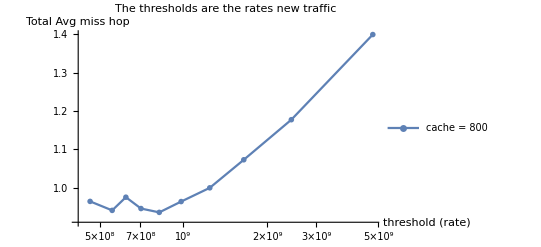

-Graphics-

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
800 | 2.97098 | 3.16667

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\total-rate-esti\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic A

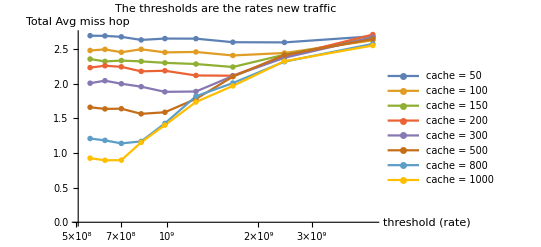

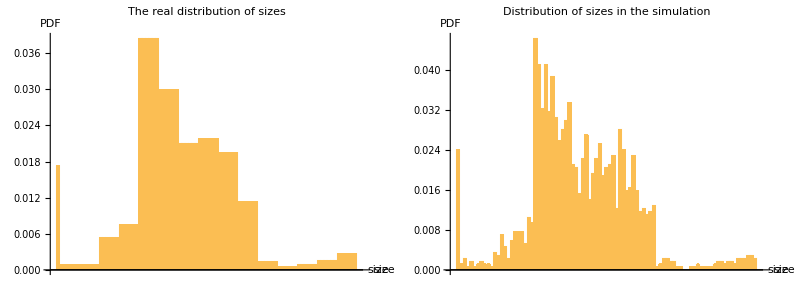

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 3.60356 | 3.39992
100 | 2.89994 | 2.41642
150 | 4.87205 | 3.84225
200 | 5.24578 | 4.14327
300 | 6.22426 | 5.20619
500 | 5.71595 | 3.76141
800 | 5.83444 | 1.85578
1000 | 3.2763 | 1.11022×10^-14

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\regular traffic\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 400M Avg      Traffic: Traffic B

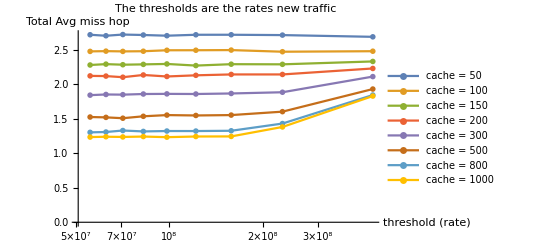

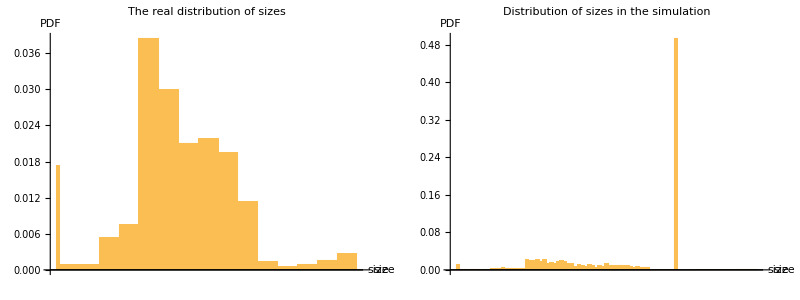

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 1.10356 | 0.829167
100 | 0.198403 | 1.11022×10^-14
150 | 0.368824 | 0.417844
200 | 0.908985 | 1.20741
300 | 0. | 0.
500 | 1.12836 | 1.79312
800 | 0. | 1.42561
1000 | 0.107216 | 1.73593

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new traffic 400M\\end time = 20.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{55658062,62593416,70927071,82556950,98284489,121805866,158245781,231309663,451566338}]]
```

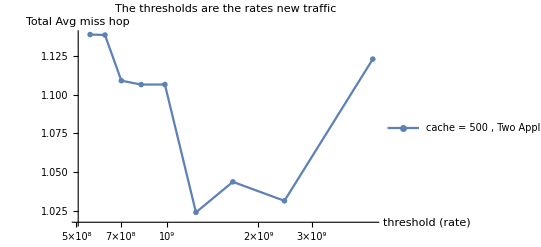

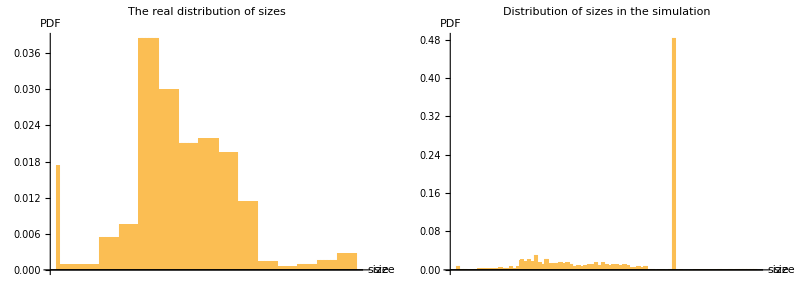

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
500 | 10.0892 | 7.339

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B hadoop\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B  Estimate Rate Window: 10 μs

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

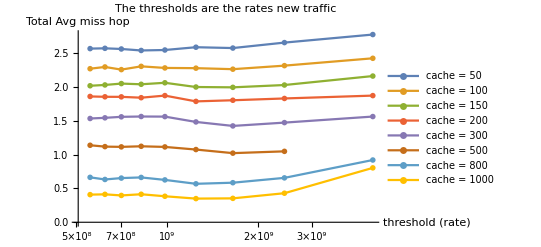

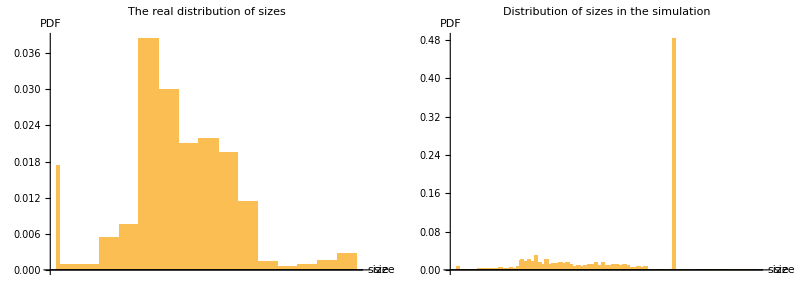

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 1.06643 | 1.26905
100 | 0.589785 | 0.740922
150 | 1.15257 | 0.
200 | 3.92975 | 3.35444
300 | 7.16187 | 5.27041
500 | 100 (1-0.878145 Min[1.0222,$Failed]) | 6.97562
800 | 14.3871 | 16.6762
1000 | 14.3551 | 29.2837

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B hadoop\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B  Estimate Rate Window: 0.5 ms

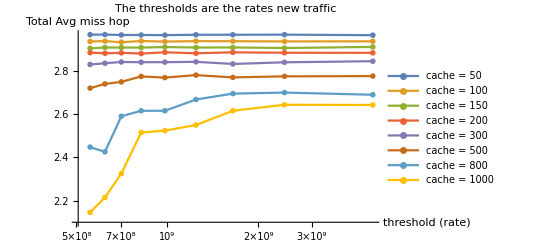

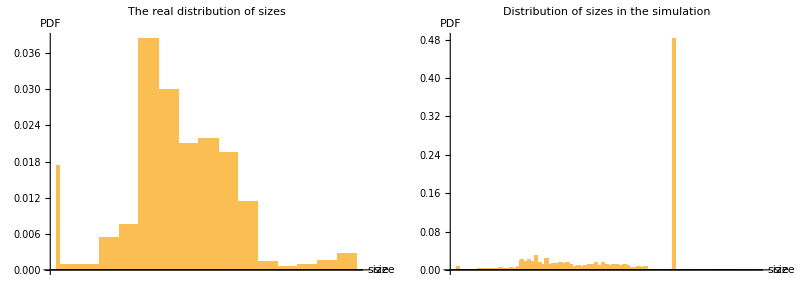

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi will be suppressed during this calculation.

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 0.0841415 | 100 (1-1/($Failed)4.02376×10^6 Min[2.44499×10^-7 $Failed,2.47341×10^-7 $Failed,2.48524×10^-7 $Failed,2.48685×10^-7 $Failed,2.49394×10^-7 $Failed,2.50277×10^-7 $Failed,2.53883×10^-7 $Failed,2.56549×10^-7 $Failed,2.56622×10^-7 $Failed])
100 | 0.122385 | 100 (1-1/($Failed)4.00418×10^6 Min[2.4456×10^-7 $Failed,2.4682×10^-7 $Failed,2.48536×10^-7 $Failed,2.48852×10^-7 $Failed,2.49739×10^-7 $Failed,2.50101×10^-7 $Failed,2.53943×10^-7 $Failed,2.56077×10^-7 $Failed,2.60795×10^-7 $Failed])
150 | 0. | 100 (1-1/($Failed)3.98603×10^6 Min[2.45388×10^-7 $Failed,2.46992×10^-7 $Failed,2.48281×10^-7 $Failed,2.49419×10^-7 $Failed,2.49744×10^-7 $Failed,2.50354×10^-7 $Failed,2.50876×10^-7 $Failed,2.51407×10^-7 $Failed,2.52503×10^-7 $Failed])
200 | 0.142685 | 100 (1-1/($Failed)4.02487×10^6 Min[2.43962×10^-7 $Failed,2.47067×10^-7 $Failed,2.48455×10^-7 $Failed,2.49403×10^-7 $Failed,2.49761×10^-7 $Failed,2.51743×10^-7 $Failed,2.52415×10^-7 $Failed,2.53034×10^-7 $Failed,2.53349×10^-7 $Failed])
300 | 0. | 100 (1-1.2029 Min[0.831323,2.46709×10^-7 $Failed,2.48402×10^-7 $Failed,2.4899×10^-7 $Failed,2.49294×10^-7 $Failed,2.52632×10^-7 $Failed,2.53779×10^-7 $Failed,2.56644×10^-7 $Failed])
500 | 0. | 100 (1-1.31243 Min[0.761944,2.46796×10^-7 $Failed,2.471×10^-7 $Failed,2.48161×10^-7 $Failed,2.5232×10^-7 $Failed,2.55151×10^-7 $Failed])
800 | 0.889042 | 100 (1-1.55951 Min[0.629677,2.49611×10^-7 $Failed,2.52265×10^-7 $Failed])
1000 | 0. | 100 (1-1.83867 Min[0.543872,2.45761×10^-7 $Failed])

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\estimate rate 0.5m\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B   Rate estimator

1

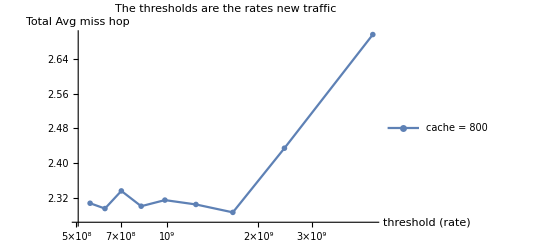

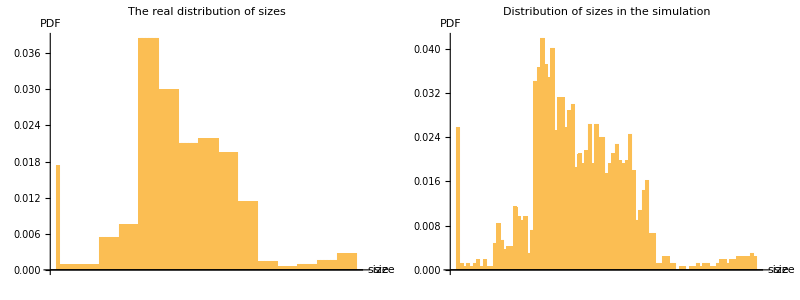

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\rate estimator check traffic A\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

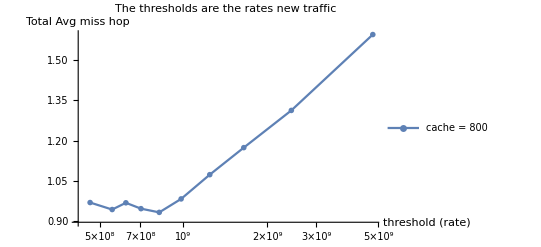

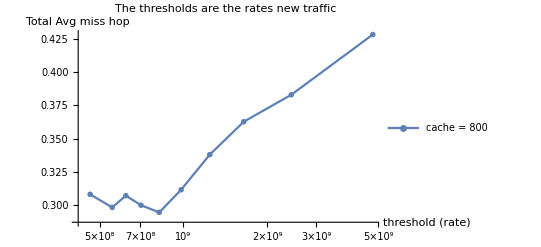

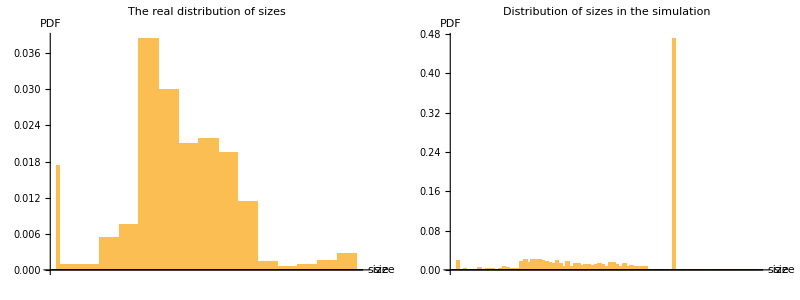

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
800 | 3.78873 | 818901538 | 4.42558 | 818901538

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\port-dest th with window2\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

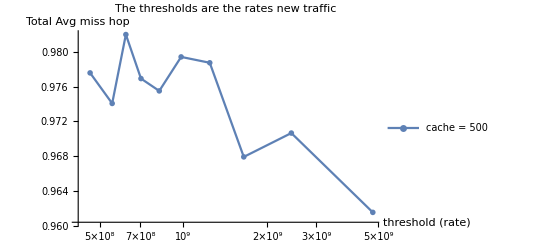

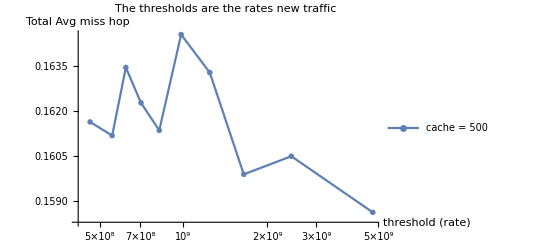

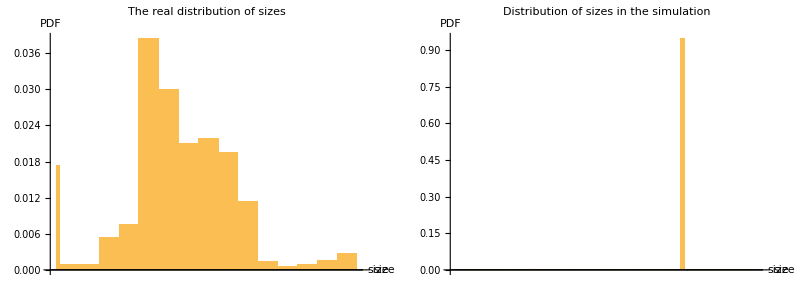

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
500 | 1.64047 | 4777534806 | 1.87607 | 4777534806

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\const rate B\\without window\\end time = 3.06s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

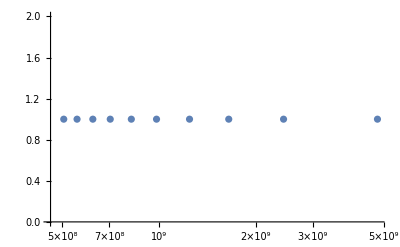

```mathematica
ListLogLinearPlot[Map[{#,1}&,{555037325/1.1,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

```mathematica
Ordering
```

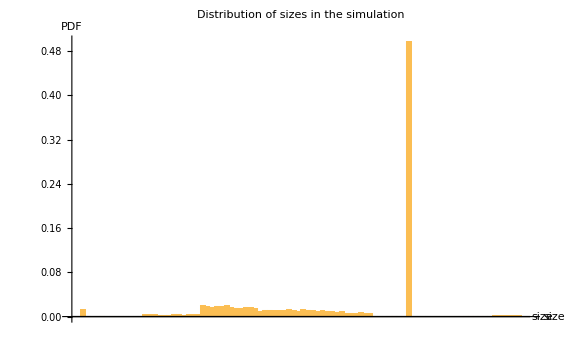

```mathematica
41000000000//N
```

4.1×10^10

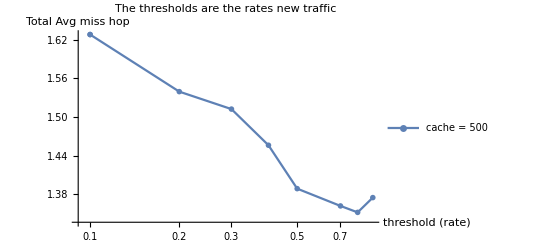

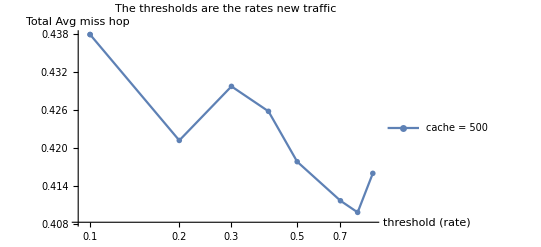

-Graphics-

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
500 | 16.9538 | 0.8 | 6.38472 | 0.8

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\without window\\traffic c2\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{0.1,0.2,0.3,0.4,0.5,0.7,0.8,0.9,0.1}]]
```